Investigating the excision radius function for the case of the BH.
The following parameters were considered: β=1, r_0=8 ,R_0=1.99, R_∞=1.9, Δ=0.05

```mathematica
β=1;r0=8;R0=1.99;Ri=2.0;Δ=0.05;
```

```mathematica
Recc[r_,c_]:=Ri(r/c)^β(1+(r/c)^(1/Δ))^(-β Δ)
Rcirc[r_]:=R0(r/r0)^β
```

Let’s root find a c for Recc that would set Recc=!=Rcirc when r=8M. In otherwords R_0=R_∞(r/c)^β(1+(r/c)^(1/Δ))^(-β Δ).

```mathematica
crule=NSolve[Recc[8,c]==R0,c,Reals][[1]]
Recc[8,c]/.crule
Recc2[r_]:=Recc[r,c]/.crule
```

{c→7.14894}

1.99

Plotting out the two functions. Expectations: They must intersect at 8M (our “initial condition”).

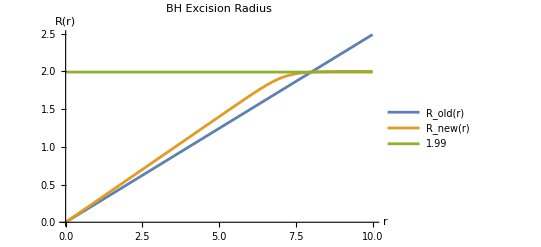

```mathematica
Plot[{Rcirc[r],Recc2[r],1.99},{r,0,10},AxesLabel->{"r","R(r)"},PlotLegends->{"R_old(r)","R_new(r)",1.99},PlotLabel->"BH Excision Radius"]
```